# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["../../quest_link_cpu"];
```

```mathematica
Import["../../../vqd.wl"]
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

#### Constants

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

#### initial states and memory allocation

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

```mathematica
DestroyAllQuregs[]
{ψexact,ψinitexact}=CreateQuregs[5,2];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

#### Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20.,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

#### The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*τ=t J/ℏ*)
```

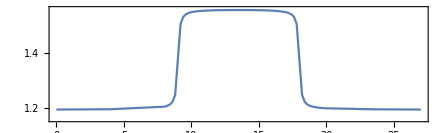

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

#### Results and analysis

```mathematica
(* get the best result with a treshold target *)
minRes[rescomp_,target_:10^-6]:=Module[{τ,δ,cres,idx,tidx,gidx=2},
cres=rescomp[[10]];
tidx=Length@cres["E"];
For[idx=2,idx<=Length@cres["E"],idx++,
If[cres["E"][[idx]]<=target,
tidx=idx;
Break[]
]
];
gidx=Last@Ordering[Length/@cres["ansatz"],2];
If[cres["E"][[gidx]]<=target,
{cres["ansatz"][[gidx]],cres["θvars"][[gidx]]}
,
{cres["ansatz"][[tidx]],cres["θvars"][[tidx]]}
]

]
```

### The matrixExp vs compiled

```mathematica
CustomGatesDefinitions={Subscript[SW, index1_,index2_][θ_]:>Subscript[U, index1,index2][{{1,0,0,0},{0,ⅇ^((ⅈ θ)/2)Cos[θ/2],-ⅈ ⅇ^((ⅈ θ)/2)Sin[θ/2],0 },{0,-ⅈ ⅇ^((ⅈ θ)/2)Sin[θ/2], ⅇ^((ⅈ θ)/2)Cos[θ/2],0 },{0,0,0,1}}]
,
Subscript[CRx, e_,n_][θ_]:>Subscript[U, e,n][{{Cos[θ/2],0,-I Sin[θ/2],0},{0,Cos[θ/2],0,I Sin[θ/2]},{-I Sin[θ/2],0,Cos[θ/2],0},{0,I Sin[θ/2],0,Cos[θ/2]}}]
,
	Subscript[CRy, e_,n_][θ_]:>Subscript[U, e,n][{{Cos[θ/2],0,-Sin[θ/2],0},{0,Cos[θ/2],0,Sin[θ/2]},{Sin[θ/2],0,Cos[θ/2],0},{0,-Sin[θ/2],0,Cos[θ/2]}}]	
}; 
CustomGatesDraw={Subscript[SW, index1_,index2_][_]:>Subscript[SWAP, index1,index2]};
```

```mathematica
summaryComp[compileresults_,ψinitexact_,ψexact_,ϵ_:10^-6]:=Module[{hbcs0,eigval,eigvec,initv,rexactcomp,τ,δ,res,ansatz,θvars,summary,idx=1,fid,fidex},
τ=0;
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
summary=Table[
{τ,δ,res}=comp;
{ansatz,θvars}=res[[4;;5]];
ApplyCircuit[ψexact,ansatz/.CustomGatesDefinitions/.θvars];
fid=CalcFidelity[ψexact,ψinitexact];
AppendTo[rexactcomp,{τ,fid}];
fidex=Last@rexactot2[[++idx]];
<|"ngates"->Length@ansatz,"ansatz"->ansatz,"θvars"->θvars,"time"->res[[1]],"cost"->res[[2]],"τ"->τ,"δ"->δ,"ϵ"->Abs[fidex-fid],"fidex"->fidex|>
,{comp, compileresults}];
{rexactcomp,summary}
]
```

Results using MatrixExp[ ]

```mathematica
rexactot2<<rexactot2.mx;
```

Compulation results

```mathematica
bcscompilecssrerun<<bcscompilecssrerun.mx;
```

```mathematica
DestroyAllQuregs[]
{ψ,ψinit}=CreateQuregs[5,2];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

```mathematica
{rexactcompcss,summarycss}=summaryComp[bcscompilecssrerun,ψinit,ψ,10^-5];
```

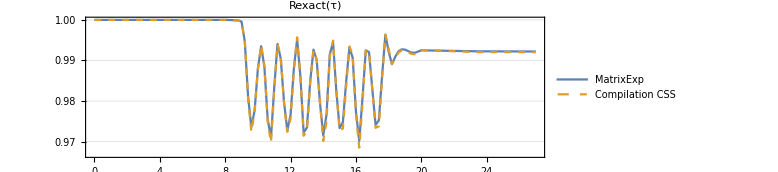

```mathematica
ListPlot[{rexactot2,rexactcompcss},Joined->{True,True},PlotStyle->{Thick,Dashed},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Automatic,None},{Range[0,27,1],None}},PlotLegends->{"MatrixExp", "Compilation CSS"},Background->White,ImageSize->500]
```

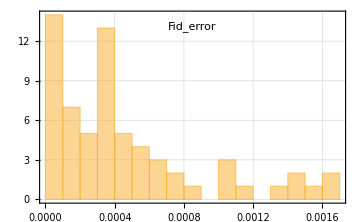

```mathematica
(* Error fidelities *)
Histogram[{summarycss[[All,"ϵ"]]},20,ChartLabels->{"Fid_error"},PlotTheme->"Detailed",Background->White,ImageSize->Medium]
```

#### Convert C[Rz(θ)] and SW[θ] to native NVC gates

```mathematica
DestroyAllQuregs[]
```

```mathematica
tonvcnative={
Subscript[C, 0][Subscript[Rx, t_][θ_]]:>Sequence@@{Subscript[CRx, 0,t][-θ/2],Subscript[Rx, t][θ/2]},
Subscript[C, 0][Subscript[Rz, t_][θ_]]:>Sequence@@{Subscript[Ry, t][π/2],Subscript[CRx, 0,t][-θ/2],Subscript[Rx, t][θ/2],Subscript[Ry, t][-π/2]},
Subscript[SW, 0,t_][θ_]:>Sequence@@{Subscript[Ry, 0][-π/2],Subscript[CRx, 0,t][θ/2],Subscript[Ry, 0][π/2],Subscript[CRy, 0,t][-π/2],Subscript[Rx, 0][θ/2],Subscript[Rx, t][-θ/2],Subscript[CRy, 0,t][π/2]}
};
```

```mathematica
(* minimize the rotation angle *)
round2pi[θ_]/;θ>=0:=With[{ϕ=Mod[θ,2π]},If[Abs[2π-ϕ]<ϕ,-(2π-ϕ),ϕ]]
replaceθ={
Subscript[Rz, q_][θ_]/;θ>=0:>Subscript[Rz, q][Chop@round2pi[θ]],
Subscript[Rx, q_][θ_]/;θ>=0:>Subscript[Rx, q][Chop@round2pi[θ]],
Subscript[Ry, q_][θ_]/;θ>=0:>Subscript[Ry, q][Chop@round2pi[θ]]
};
```

```mathematica
swapCRx[g_]:=Module[{i,j,θ,circ},
{i,j,θ}=g/.Subscript[CRx, p_,q_][t_]:>{p,q,t};
circ=Which[
(i==0)&&(j>0),
{Subscript[CRx, 0,j][θ]}
,
(i>0)&&(j>0)
,
{Subscript[SWAP, 0,i],Subscript[CRx, 0,j][θ],Subscript[SWAP, 0,i]}/.swaprep
,
(*i>0, j=0*)
True,
{Subscript[Ry, i][π/2],Subscript[Rx, i][π],Subscript[Ry, j][π/2],Subscript[Rx, j][π],Subscript[CRx, 0,i][θ],Subscript[Ry, i][π/2],Subscript[Rx, i][π],Subscript[Ry, j][π/2],Subscript[Rx, j][π]}
];
Sequence@@circ
]
```

```mathematica
(* simple gate merges *)
mergeNVCGates[longcirc_]:=Module[{circ,circcol,a,b,c,d,e,f,i,j,slen,k,l,θmerge={},deleted=0},
circ=longcirc;
While[True,
slen=Length@circ;
circcol=GetCircuitColumns[circ];
(* simplify parametric gates *)
circcol=circcol//.{
{a___,{b___,Subscript[Rx, j_][θ1_],c___},{d___,Subscript[Rx, j_][θ2_],e___},f___}:>{a,{b,Subscript[Rx, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[Ry, j_][θ1_],c___},{d___,Subscript[Ry, j_][θ2_],e___},f___}:>{a,{b,Subscript[Ry, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[Rz, j_][θ1_],c___},{d___,Subscript[Rz, j_][θ2_],e___},f___}:>{a,{b,Subscript[Rz, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[CRx, i_,j_][θ1_],c___},{d___,Subscript[CRx, i_,j_][θ2_],e___},f___}:>{a,{b,Subscript[CRx, i,j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[CRy, i_,j_][θ1_],c___},{d___,Subscript[CRy, i_,j_][θ2_],e___},f___}:>{a,{b,Subscript[CRy, i,j][θ1+θ2],c},{d,e},f}
};
circ=DeleteElements[Flatten[circcol]/.replaceθ,{Subscript[_, __][0],Subscript[_, __][0.]}];
If[Length@circ==slen,Break[]];
];
circ
]
```

```mathematica
summarycss2=Table[
circ=mergeNVCGates[sum["ansatz"]/.sum["θvars"]/.tonvcnative];
AssociateTo[sum,"circnvc"->circ]
,{sum,summarycss}];
```

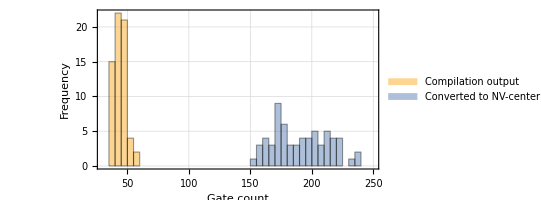

~/vqd/img/bcsgates.pdf

```mathematica
Histogram[{summarycss2[[All,"ngates"]],Length/@summarycss2[[All,"circnvc"]]},50,
FrameStyle->Directive[Thick,Black,16],
Background->White,
ChartStyle->Directive[EdgeForm[Black], Automatic],
PlotTheme->"Detailed",
ImageSize->400,
AspectRatio->0.5,
Frame->True,
FrameLabel->{"Gate count","Frequency"},
LabelStyle->{"Gate counts",17,FontFamily->"FreeSerif"},
ChartLegends->Placed[{"Compilation output","Converted to NV-center native gates"},{0.6,0.75}],PlotRange->{{30,250},Automatic}]
Export["~/vqd/img/bcsgates.pdf",%]
```

Total native gates until the end

```mathematica
Total[Length/@summarycss2[[All,"circnvc"]]]
```

12187

Total gates (output from compilation) until the end

```mathematica
Total[summarycss2[[All,"ngates"]]]
```

2788

#### Converting to NVC native gates

Realistic setting

```mathematica
Options[NVCenterDelft]={
qubitsNum->5,
T1-> <|0-> 3600,1->60,2->60,3->60,4->60 |>,
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9|>,
FreqWeakZZ->3,
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500|>,
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3|>,
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 |>,
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98|>,
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99 |>,
FidSingleZ->  <| 0->1,1-> 1,2->1, 3->1,4->1 |>,
EFSingleXY->{0.75,0.25},
EFCRot->{0.9,0.1},
FidInit-> 0.999,
DurInit->2*10^-3,
FidMeas->0.946,
DurMeas->2*10^-5
};
```

```mathematica
noisyBCS[ρ_,ρinit_,ψinit_,vdopt_:{}]:=Module[{τ,rexactnoisy,noisycirc,fid},
τ=0;
CloneQureg[ρ,ρinit];
rexactnoisy={{0,1}};
Table[
noisycirc=ExtractCircuit@InsertCircuitNoise[List/@sum["circnvc"],NVCenterDelft[Sequence@@vdopt]];
noisycirc=DeleteCases[DeleteCases[noisycirc,Subscript[__, __][0.]],Subscript[__, __][0]];
ApplyCircuit[ρ,noisycirc/.CustomGatesDefinitions];
fid=CalcFidelity[ρ,ψinit];
τ+=sum["δ"];
AppendTo[rexactnoisy,{τ,fid}];
(*<|"τ"->τ,"δ"->sum["δ"],"fidnoisy"->fid,"ϵnoisy"->Abs[sum["fidexact"]-fid]|>*)
,{sum, summarycss2}];
rexactnoisy
]
```

### Simulations on various noise scenarios

Several scenarios :
1)  Exact unitary using MatrixExp[]
2) Checking using the resulting CSS compilation
3) Realistic numbers from Mohammed 
4) Perfect gates with realistic decoherence
5) Extremely high gates fidelity 99.999, realistic decoherence
6) 10x longer decoherece with excellent gates 99.999

```mathematica
labels=<|
1->"Exact propagator",
2->"Subspace compilation",
3->"Realistic noise",
4->"Perfect gate",
5->"Gates fidelity 99.999",
6->"10x of T1,T2",
7->"Gates fidelity 99.999, 10x of T1,T2",
8->"Gates fidelity 99.999, 10x of T1,T2, no cross-talk"
|>;
```

```mathematica
(*initialisation: exact groundstate*)
DestroyAllQuregs[];
ψinit=CreateQureg[5];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
initmat=(List/@initv).Conjugate[{initv}];
{ρ,ρinit}=CreateDensityQuregs[5,2];
SetQuregMatrix[ρinit,initmat];
SetQuregMatrix[ψinit,initv];
```

```mathematica
(* Options on excellent gates and very long decoherence: 10x better *)
optgates = {FidCRot -> Association[{# -> .99999} & /@ Range[4]], FidSingleXY -> Association[{# -> .99999} & /@ Range[0, 4]]};
optdec = {T1 -> <|0 -> 36000, 1 -> 600, 2 -> 600, 3 -> 600, 4 -> 600 |>, T2 -> <|0 -> 15, 1 -> 100, 2 -> 100, 3 -> 100, 4 -> 90|>};

bcsfidelities = <|
   1 -> rexactot2,
   2 -> rexactcompcss,
   3 -> noisyBCS[ρ, ρinit, ψinit],
   4 -> noisyBCS[ρ, ρinit, ψinit, {EFSingleXY -> {0., 0.}, EFCRot -> {0., 0.}}],
   5 -> noisyBCS[ρ, ρinit, ψinit, optgates],
   6 -> noisyBCS[ρ, ρinit, ψinit, optdec],
   7 -> noisyBCS[ρ, ρinit, ψinit, Join[optgates, optdec]],
   8 -> noisyBCS[ρ, ρinit, ψinit, Join[optgates, optdec, {FreqWeakZZ -> False}]]
   |>;
```

```mathematica
plotstyles={PlotRange->All,
PlotTheme->"Scientific",
AspectRatio->.6,
Background->White,
ImageSize->600,
Frame->True,
FrameStyle->Directive[Thick,Black,17],
BaseStyle->{16},
GridLines->{τs,None},
GridLinesStyle->Directive[GrayLevel[0.8,0.8],Thin]
};
```

```mathematica
gdense<<gdense.mx;
```

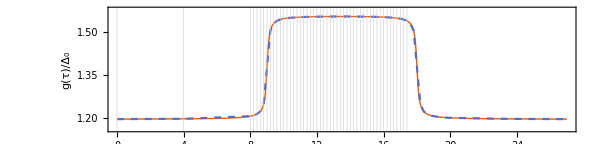

```mathematica
keys={"analytic","discretised"};
bcs1=ListPlot[
{gdense,Transpose@{τs,gvals}},
PlotRange->{1.16,1.58},
Joined->{True,True},
AspectRatio->0.24,
PlotStyle->{Thick,Dashed},
PlotLegends->Placed[LineLegend[keys,Spacings->0],{.15,.25}],
FrameLabel->{{"g(τ)/Δ_0",None},{None,None}},
ImagePadding->{{58,10},{0,0}},
Sequence@@plotstyles]
```

The compilation outputs

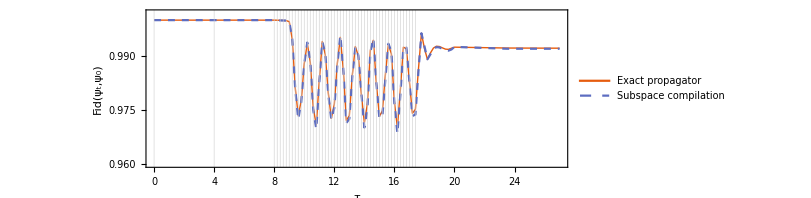

```mathematica
keys={1,2};
bcs2=ListPlot[
bcsfidelities/@keys,
Joined->ConstantArray[True,Length@keys],
PlotStyle->Join[{Thick},ConstantArray[Dashed,Length@keys-1]],
PlotLegends->Placed[LineLegend[labels/@keys,Spacings->0],{.22,.2}],
PlotRange->{Automatic,{0.96,1.002}},
AspectRatio->.33,
ImagePadding->{{58,10},{50,0}},
FrameLabel->{"τ","Fid(ψ_t,ψ_0)"},
Sequence@@plotstyles
]
```

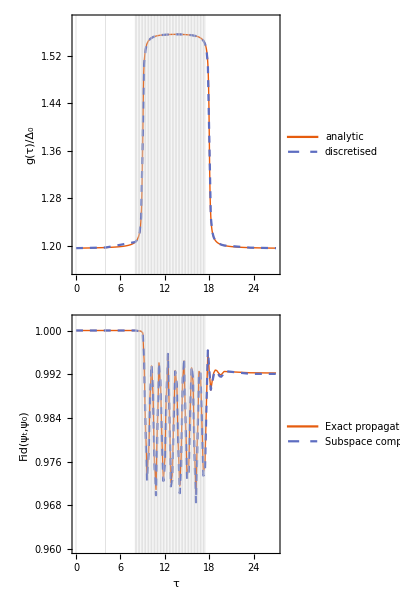

```mathematica
Column[{bcs1,bcs2},Spacings->-0.1]
(*Export["~/vqd/img/quench.pdf",%]*)
```

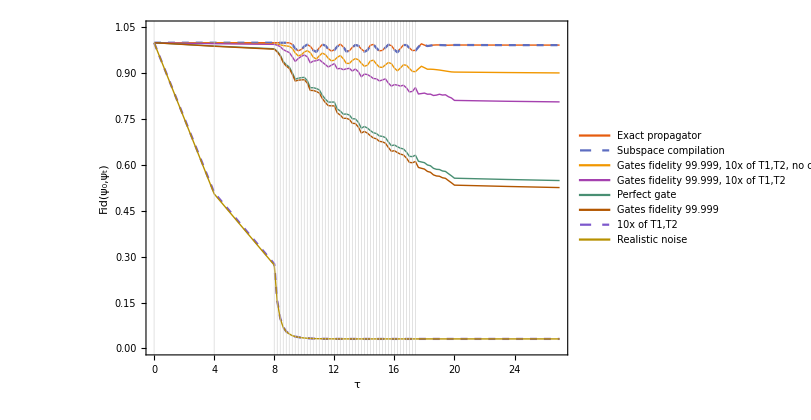

```mathematica
keys={1,2,8,7,4,5,6,3};
bcs3=ListPlot[
bcsfidelities/@keys,
Joined->ConstantArray[True,Length@bcsfidelities],
PlotStyle->{Thick,Dashed,Thick,Thick,Thick,Thick,Dashed,Thick},
AspectRatio->0.7,
PlotLegends->Placed[LineLegend[labels/@keys,Spacings->0,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.63,0.25}],
ImagePadding->{{58,10},{50,0}},
FrameLabel->{"τ","Fid(ψ_0,ψ_t)"},
PlotRange->{{0,27},{0.0,1.05}},
BaseStyle->{14},
Sequence@@plotstyles
]
(*Export["~/vqd/img/bcsall.pdf",%]*)
```